# Final Lecture Demo File

## Some preliminary materials

```mathematica
$Assumptions = {V0>0,r>0}; (*This will allow for quantities such as √(V0^2) to be simplified as V0*)
f[x_,y_,z_] = -2y + y z;
g[x_,y_,z_] = x -x z;
h[x_,y_,z_] = x y;
F[x_,y_,z_] = {f[x,y,z],g[x,y,z],h[x,y,z]}
```

{-2 y+y z,x-x z,x y}

## Local Analysis

```mathematica
Solve[F[x,y,z]=={0,0,0},{x,y,z}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→0,y→0},{x→0,z→2},{y→0,z→1}}

```mathematica
DF[x_,y_,z_] = Grad[F[x,y,z],{x,y,z}]
```

{{0,-2+z,y},{1-z,0,-x},{y,x,0}}

## Checking that V(x,y,z) = x^2+2 y^2 + z^2 = V0^2 is conserved

```mathematica
V[x_,y_,z_] = x^2 + 2 y^2 + z^2
```

x^2+2 y^2+z^2

```mathematica
gradV = Grad[V[x,y,z],{x,y,z}]
```

{2 x,4 y,2 z}

Now, we would like to calculate dV/dt = V_x dx/dt + V_y dy/dt+ V_z dz/dt = ▽V·F⃗(x,y,z)

```mathematica
(*Calculate dV/dt*)
```

```mathematica
gradV.F[x,y,z]//Simplify
```

0

## The (x,y) reduced system

### Top Half System Definition

```mathematica
fTop[x_,y_,V0_]  = f[x,y,z]/.z->Sqrt[V0^2-x^2-2 y^2];
gTop[x_,y_,V0_] = g[x,y,z]/.z->Sqrt[V0^2- x^2-2 y^2];
FTop[x_,y_,V0_] = {fTop[x,y,V0],gTop[x,y,V0]}; (*This last line is the vector version*)
```

```mathematica
Grad[FTop[x,y,V0],{x,y}]
```

{{-(x y)/(√(V0^2-x^2-2 y^2)),-2-(2 y^2)/(√(V0^2-x^2-2 y^2))+√(V0^2-x^2-2 y^2)},{1+x^2/(√(V0^2-x^2-2 y^2))-√(V0^2-x^2-2 y^2),(2 x y)/(√(V0^2-x^2-2 y^2))}}

#### Local Analysis of the Top Half

```mathematica
eqPts=Solve[FTop[x,y,V0]=={0,0},{x,y}]
```

{{x→0,y→0},{x→-√(-1+V0^2),y→0},{x→√(-1+V0^2),y→0},{x→0,y→-(√(-4+V0^2))/(√2)},{x→0,y→(√(-4+V0^2))/(√2)}}

```mathematica
DFTop[x_,y_,V0_] = Grad[FTop[x,y,V0],{x,y}]
```

{{-(x y)/(√(V0^2-x^2-2 y^2)),-2-(2 y^2)/(√(V0^2-x^2-2 y^2))+√(V0^2-x^2-2 y^2)},{1+x^2/(√(V0^2-x^2-2 y^2))-√(V0^2-x^2-2 y^2),(2 x y)/(√(V0^2-x^2-2 y^2))}}

#### Equilibrium Point 1:

```mathematica
(*Define the Jacobian at (0,0)*)
J1 = DFTop[0,0,V0]
```

{{0,-2+√(V0^2)},{1-√(V0^2),0}}

```mathematica
(*Determine the Eigenvalues*)
ev1= Eigenvalues[J1]//FullSimplify
```

{-√(-(-2+V0) (-1+V0)),√(-(-2+V0) (-1+V0))}

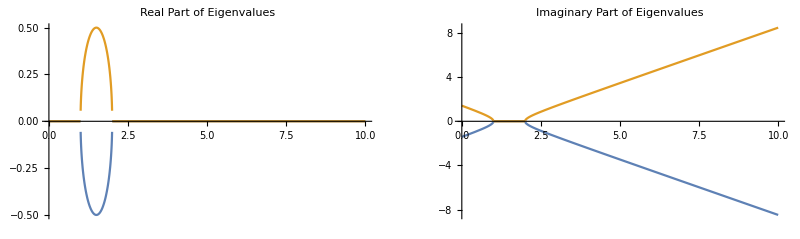

```mathematica
(*Plot the eigenvalues*)
p1 = Plot[Evaluate[Re[ev1]],{V0,0,10},PlotLabel->"Real Part of Eigenvalues"];
p2 = Plot[Evaluate[Im[ev1]],{V0,0,10},PlotLabel->"Imaginary Part of Eigenvalues"];
GraphicsGrid[{{p1,p2}}]
```

#### Equilibrium Point 2:

```mathematica
(*Define the Jacobian at (√(V0^2-1),0)*)
J2 = DFTop[Sqrt[V0^2-1],0,V0]
```

{{0,-1},{-1+V0^2,0}}

```mathematica
(*Determine the Eigenvalues*)
ev2= Eigenvalues[J2]
```

{-√(1-V0^2),√(1-V0^2)}

```mathematica
(*Plot the eigenvalues*)
p1 = Plot[Evaluate[Re[ev2]],{V0,0,10},PlotLabel->"Real Part of Eigenvalues"];
p2 = Plot[Evaluate[Im[ev2]],{V0,0,10},PlotLabel->"Imaginary Part of Eigenvalues"];
GraphicsGrid[{{p1,p2}}]
```

#### Equilibrium Point 3:

```mathematica
(*Define the Jacobian at (0,√(V0^2-4)/Sqrt[2])*)
J3 = DFTop[0,Sqrt[V0^2-4]/Sqrt[2],V0]
```

{{0,1/2 (4-V0^2)},{-1,0}}

```mathematica
(*Determine the Eigenvalues*)
ev3= Eigenvalues[J3]
```

{-(√(-4+V0^2))/(√2),(√(-4+V0^2))/(√2)}

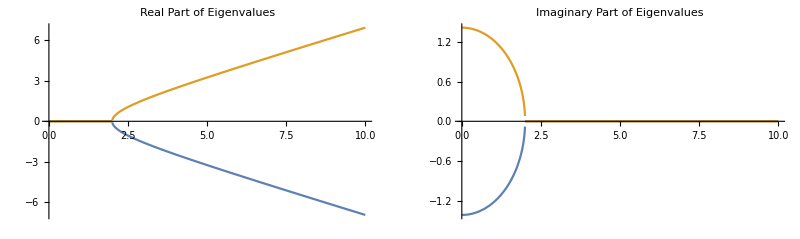

```mathematica
(*Plot the eigenvalues*)
p1 = Plot[Evaluate[Re[ev3]],{V0,0,10},PlotLabel->"Real Part of Eigenvalues"];
p2 = Plot[Evaluate[Im[ev3]],{V0,0,10},PlotLabel->"Imaginary Part of Eigenvalues"];
GraphicsGrid[{{p1,p2}}]
```

#### Alternative Approach 1:

```mathematica
Manipulate[StreamPlot[FTop[x,y,V0],{x,-V0,V0},{y,-V0,V0}],{V0,0.1,3}]
DSolve[D[y[x],x]==gTop[x,y[x],V0]/fTop[x,y[x],V0],y[x],x]
```

{{y[x]→-√(-4-x^2-2 √(4+V0^2+x^2-4 C[1])+2 C[1])},{y[x]→√(-4-x^2-2 √(4+V0^2+x^2-4 C[1])+2 C[1])},{y[x]→-√(-4-x^2+2 √(4+V0^2+x^2-4 C[1])+2 C[1])},{y[x]→√(-4-x^2+2 √(4+V0^2+x^2-4 C[1])+2 C[1])}}

#### Alternative Approach 2:

```mathematica
coordChangeRules = {x-> r Sin[θ]Cos[ϕ],y-> r/Sqrt[2] Sin[θ]Sin[ϕ],z->r Cos[θ]};
```

```mathematica
rotMat = {{r Cos[θ]Cos[ϕ] , -r Sin[θ]Sin[ϕ]},{r/Sqrt[2] Cos[θ]Sin[ϕ] , r/Sqrt[2] Sin[θ]Cos[ϕ]}};
rotMat//MatrixForm
```

(r Cos[θ] Cos[ϕ] | -r Sin[θ] Sin[ϕ]
(r Cos[θ] Sin[ϕ])/(√2) | (r Cos[ϕ] Sin[θ])/(√2))

```mathematica
newSys[r_,θ_,ϕ_]=FullSimplify[ Inverse[rotMat].FTop[x,y,r]/.coordChangeRules]
```

{-1/4 r √(1+Cos[2 θ]) Sin[2 ϕ] Tan[θ],-(-4+3 r √(Cos[θ]^2)+r √(Cos[θ]^2) Cos[2 ϕ])/(2 √2)}

```mathematica
Manipulate[StreamPlot[newSys[r,θ,ϕ],{θ,0,Pi/2},{ϕ,-Pi,Pi},ImageSize->400],{r,0,3}]
```

```mathematica
Manipulate[
sp=StreamPlot[newSys[r,θ,ϕ],{θ,0,Pi/2},{ϕ,-Pi,Pi},ImageSize->400];
sp3d=Graphics3D[sp[[1]]/.Arrow[z_]:>Arrow[z/.{x_Real,y_Real}:>{r Sin[x] Cos[y],r/Sqrt[2]  Sin[x] Sin[y],r Cos[x]}],ImageSize->400];
Row[{sp,sp3d},Spacer[5]],{r,.1,3}]
```